## Analytic

## 1. Ring in analytic triaxial NFW potential

### r0 = 50 kpc (gets converted to code units offset option = 0 (no random radial offsets) Ne = 1 ( number of particles in a ring) nbins = 4 (number of bins for power spectrum) N = 100,000 timesteps dt = 1,000,000 years (gets converted to code units) potential initialization parameter: 417 km/sec, 36.54 kpc, phi = 90 degrees, q1=q2=1, qz = 0.94 initial velocity = 0.75 * centripetal velocity period = ??? adjust periods leapfrog with ChplUltra units

#### Import coordinates

```mathematica
anly1posxy = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/NFW-ring/NFW-anly-ring-1/pos-vel.csv",{"Data",1;;100000,6;;7}];
anly1posyz = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/NFW-ring/NFW-anly-ring-1/pos-vel.csv",{"Data",70000;;100000,7;;8}];
anly1period1 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/NFW-ring/NFW-anly-ring-1/pos-vel.csv",{"Data",1;;22300,6;;7}];
anly1period2 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/NFW-ring/NFW-anly-ring-1/pos-vel.csv",{"Data",22300;;44600,6;;7}];
anly1period3 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/NFW-ring/NFW-anly-ring-1/pos-vel.csv",{"Data",44600;;66950,6;;7}];
anly1period4 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/NFW-ring/NFW-anly-ring-1/pos-vel.csv",{"Data",66950;;89000,6;;7}];
anly1period5 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/NFW-ring/NFW-anly-ring-1/pos-vel.csv",{"Data",89500;;100000,6;;7}];
```

#### Position graph 1

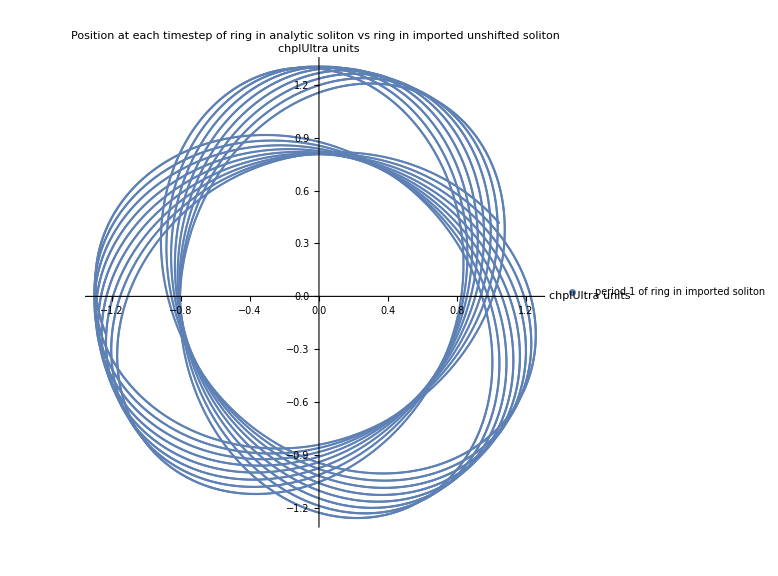

```mathematica
anly1posxygraph = ListPlot[{},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"period 1 of ring in imported soliton ","period 4 of ring in imported soliton"},AxesLabel->{"chplUltra units","chplUltra units"}, PlotLabel->"Position at each timestep of ring in analytic soliton vs ring in imported unshifted soliton"]
```

## Imported